```mathematica
SetDirectory[NotebookDirectory[]]
files = FileNames["*.tab"]
```

/home/benjamin/Documents/Uni/FP2/0407-Optisches Pumpen/data/part1

{01-63.6mA-33.3C.tab,02-70.0mA-33.3C.tab,03-70.0mA-30.0C.tab,04-63.6mA-30.0C.tab,05-63.6mA-36.0C.tab,06-70.0mA-36.0C.tab,07-63.6mA-33.7C.tab,08-63.6mA-33.6C.tab,09-63.6mA-33.3C.tab,10-63.6mA-33.1C.tab,11-63.6mA-32.8C.tab,12-63.6mA-32.6C.tab}

```mathematica
datas = Import[#]&/@ files;
datas = Drop[#, 1]&/@ datas;
```

```mathematica
A=Transpose[{#[[All,1]],#[[All,2]]}]&/@ datas;
B=Transpose[{#[[All,1]],#[[All,3]]}]&/@ datas;
```

```mathematica
ABs = Transpose[{A, B}];
```

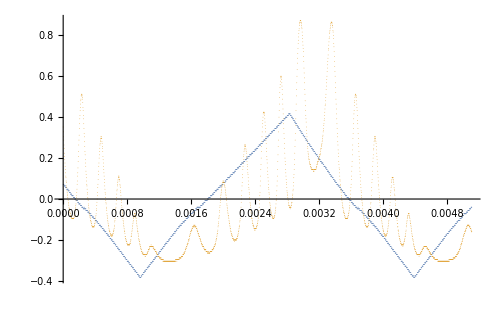
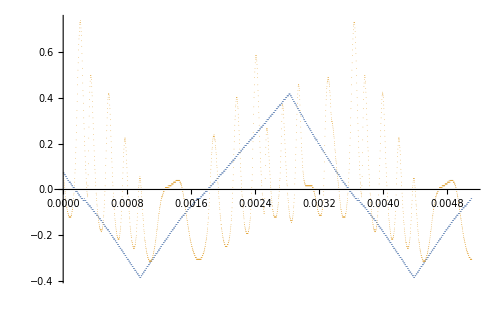
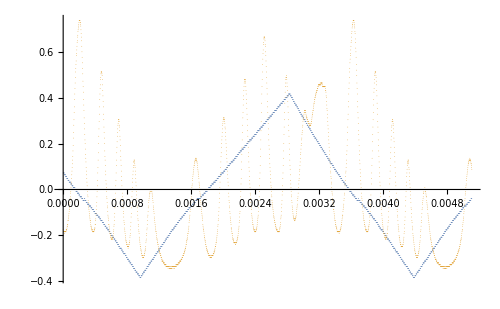
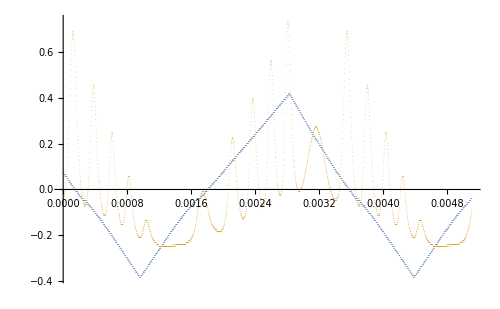
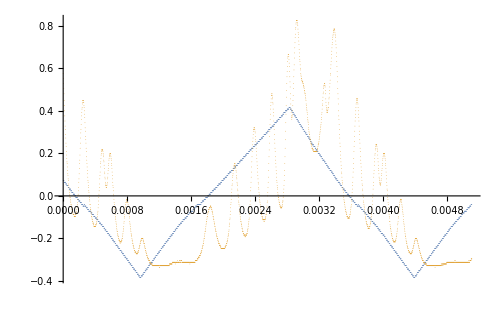
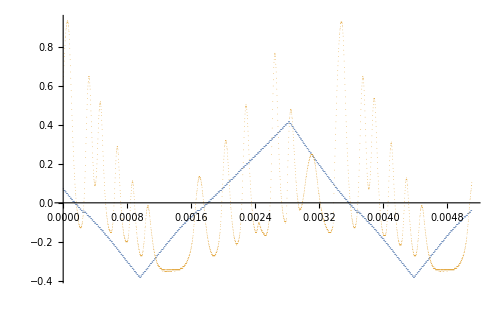
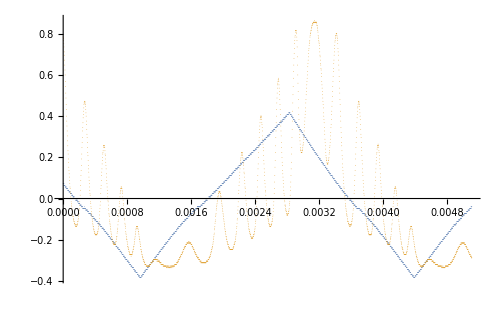
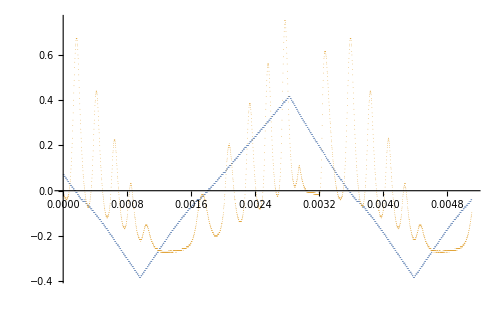

```mathematica
ListPlot[#, ImageSize->500,PlotStyle->{PointSize[0.0001]}]&/@ ABs
```

```mathematica
{#[[1]], #[[2]]} & /@ Transpose[{{1, 2, 3}, {4, 5, 6}}]
```

{{1,4},{2,5},{3,6}}